## Energy Function - A

```mathematica
ClearAll["Global`*"]
```

```mathematica
figPath="/Users/basavyr/Documents/Work/PhD/phdthesis/Chapters/Figures";
export[object_,name_]:=Export[StringTemplate["``/``.pdf"][figPath,name],object,ImageResolution->1200];
```

```mathematica
Hprime[x2_,phi2_,I_,u_,v0_]:=x2^2(1-u*Cos[phi2]^2-v0/I Sin[phi2])+u*I^2*Cos[phi2]^2+2v0*I*Sin[phi2];
```

```mathematica
IConst=19/2;
A1Const=1/(2*10);
A2Const=1/(2*40);
A3Const=1/(2*20);
thetaConst=70*π/180;
jConst=11/2;
```

```mathematica
u[A1_,A3_,A_]:=(A3-A1)/A;
A[I_,j_,theta_,A1_,A2_]:=A2(1-j*Sin[theta]/I)-A1;
v0[j_,theta_,A1_,A_]:=(-A1*j*Cos[theta])/A;
```

```mathematica
AConst[I_]:=A[I,jConst,thetaConst,A1Const,A2Const];
uConst[I_]:=u[A1Const,A3Const,AConst[I]];
v0Const[I_]:=v0[jConst,thetaConst,A1Const,AConst[I]];
HprimeMin[I_]:=N[-2*v0Const[I]*I];
```

```mathematica
opts={Frame->True,Axes->False,AspectRatio->0.85,ImageSize->420,FrameStyle->Directive[Black,Thick],LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"}};
```

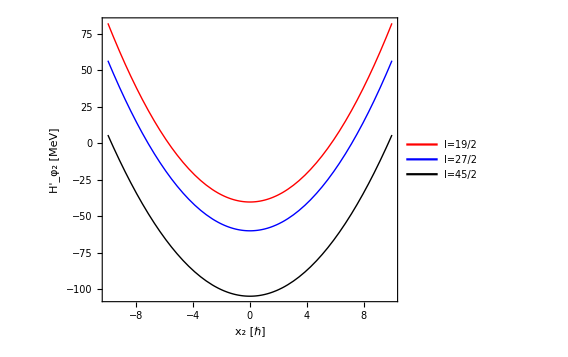

```mathematica
p1=Plot[{Hprime[x,-π/2,19/2,uConst[19/2],v0Const[19/2]],Hprime[x,-π/2,27/2,uConst[27/2],v0Const[27/2]],Hprime[x,-π/2,45/2,uConst[45/2],v0Const[45/2]]},{x,-10,10},Evaluate[opts],FrameLabel->{"x_2 [ℏ]","H'_φ_2 [MeV]"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{"I=19/2","I=27/2","I=45/2"},{0.35,0.75}]];
Show[p1]
export[p1,"Energy-Function-New-Boson-A1-phi2-const"];
```

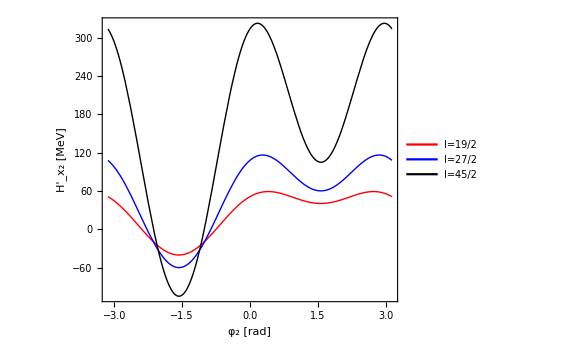

```mathematica
p2=Plot[{Hprime[0,x,19/2,uConst[19/2],v0Const[19/2]],Hprime[0,x,27/2,uConst[27/2],v0Const[27/2]],Hprime[0,x,45/2,uConst[45/2],v0Const[45/2]]},{x,-π,π},Evaluate[opts],FrameLabel->{"φ_2 [rad]","H'_x_2 [MeV]"},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{"I=19/2","I=27/2","I=45/2"},{0.7,0.18}]];
Show[p2]
export[p2,"Energy-Function-New-Boson-A1-x2-const"];
```